```mathematica
Get["NeutronBeam/MethodTesting.m"];
```

Set::wrsym: Symbol pmax is Protected.

# phiDV and p integration

## First glimpse

### without p boundaries

```mathematica
t0=AbsoluteTime[];
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVAndMomentumInt[0.,0.,0.,{0.,Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Method->"GlobalAdaptive"]
t1=AbsoluteTime[];
(t1-t0)
```

{1070.61,{{{593641.,0.},{806502.,0.},{380780.,0.},{1.15682×10^6,0.},{30463.7,0.},{593641.,1.12648},{593641.,-1.12648},{593641.,2.98038},{593641.,-2.98038},{1.15682×10^6,2.98038},{1.15682×10^6,-2.98038},{30463.7,-2.98038},{30463.7,2.98038},{185069.,-2.16219},{185069.,2.16219},{1.00221×10^6,-2.16219},{1.00221×10^6,2.16219},{296821.,0.},{403251.,0.},{190390.,0.},{578409.,0.},{15231.9,0.},{296821.,1.12648},{296821.,-1.12648},{296821.,2.98038},{296821.,-2.98038},{578409.,2.98038},{578409.,-2.98038},{15231.9,-2.98038},{15231.9,2.98038},{92534.7,-2.16219},{92534.7,2.16219},{501107.,-2.16219},{501107.,2.16219},{890462.,0.},{996893.,0.},{784031.,0.},{1.17205×10^6,0.},{608873.,0.},{890462.,1.12648},{890462.,-1.12648},{890462.,2.98038},{890462.,-2.98038},{1.17205×10^6,2.98038},{1.17205×10^6,-2.98038},{608873.,-2.98038},{608873.,2.98038},{686176.,-2.16219},{686176.,2.16219},{1.09475×10^6,-2.16219},{1.09475×10^6,2.16219},{148410.,0.},{201626.,0.},{95195.,0.},{289205.,0.},{7615.93,0.},{148410.,1.12648},{148410.,-1.12648},{148410.,2.98038},{148410.,-2.98038},{289205.,2.98038},{289205.,-2.98038},{7615.93,-2.98038},{7615.93,2.98038},{46267.3,-2.16219},{46267.3,2.16219},{250553.,-2.16219},{250553.,2.16219},{445231.,0.},{498446.,0.},{392016.,0.},{586025.,0.},{304437.,0.},{445231.,1.12648},{445231.,-1.12648},{445231.,2.98038},{445231.,-2.98038},{586025.,2.98038},{586025.,-2.98038},{304437.,-2.98038},{304437.,2.98038},{343088.,-2.16219},{343088.,2.16219},{547374.,-2.16219},{547374.,2.16219},{371026.,0.},{397633.,0.},{344418.,0.},{441423.,0.},{300629.,0.},{371026.,1.12648},{371026.,-1.12648},{371026.,2.98038},{371026.,-2.98038},{441423.,2.98038},{441423.,-2.98038},{300629.,-2.98038},{300629.,2.98038},{319954.,-2.16219},{319954.,2.16219},{422097.,-2.16219},{422097.,2.16219},{519436.,0.},{546044.,0.},{492829.,0.},{589833.,0.},{449039.,0.},{519436.,1.12648},{519436.,-1.12648},{519436.,2.98038},{519436.,-2.98038},{589833.,2.98038},{589833.,-2.98038},{449039.,-2.98038},{449039.,2.98038},{468365.,-2.16219},{468365.,2.16219},{570508.,-2.16219},{570508.,2.16219},{742052.,0.},{795267.,0.},{688836.,0.},{882846.,0.},{601257.,0.},{742052.,1.12648},{742052.,-1.12648},{742052.,2.98038},{742052.,-2.98038},{882846.,2.98038},{882846.,-2.98038},{601257.,-2.98038},{601257.,2.98038},{639909.,-2.16219},{639909.,2.16219},{844195.,-2.16219},{844195.,2.16219},{1.03887×10^6,0.},{1.09209×10^6,0.},{985657.,0.},{1.17967×10^6,0.},{898078.,0.},{1.03887×10^6,1.12648},{1.03887×10^6,-1.12648},{1.03887×10^6,2.98038},{1.03887×10^6,-2.98038},{1.17967×10^6,2.98038},{1.17967×10^6,-2.98038},{898078.,-2.98038},{898078.,2.98038},{936729.,-2.16219},{936729.,2.16219},{1.14102×10^6,-2.16219},{1.14102×10^6,2.16219},{667846.,0.},{694454.,0.},{641239.,0.},{738244.,0.},{597449.,0.},{667846.,1.12648},{667846.,-1.12648},{667846.,2.98038},{667846.,-2.98038},{738244.,2.98038},{738244.,-2.98038},{597449.,-2.98038},{597449.,2.98038},{616775.,-2.16219},{616775.,2.16219},{718918.,-2.16219},{718918.,2.16219},{816257.,0.},{842864.,0.},{789649.,0.},{886654.,0.},{745860.,0.},{816257.,1.12648},{816257.,-1.12648},{816257.,2.98038},{816257.,-2.98038},{886654.,2.98038},{886654.,-2.98038},{745860.,-2.98038},{745860.,2.98038},{765185.,-2.16219},{765185.,2.16219},{867328.,-2.16219},{867328.,2.16219},{630744.,0.},{644048.,0.},{617440.,0.},{665943.,0.},{595545.,0.},{630744.,1.12648},{630744.,-1.12648},{630744.,2.98038},{630744.,-2.98038},{665943.,2.98038},{665943.,-2.98038},{595545.,-2.98038},{595545.,2.98038},{605208.,-2.16219},{605208.,2.16219},{656280.,-2.16219},{656280.,2.16219},{704949.,0.},{718253.,0.},{691645.,0.},{740148.,0.},{669750.,0.},{704949.,1.12648},{704949.,-1.12648},{704949.,2.98038},{704949.,-2.98038},{740148.,2.98038},{740148.,-2.98038},{669750.,-2.98038},{669750.,2.98038},{679413.,-2.16219},{679413.,2.16219},{730485.,-2.16219},{730485.,2.16219},{612193.,0.},{618845.,0.},{605541.,0.},{629792.,0.},{594593.,0.},{612193.,1.12648},{612193.,-1.12648},{612193.,2.98038},{612193.,-2.98038},{629792.,2.98038},{629792.,-2.98038},{594593.,-2.98038},{594593.,2.98038},{599425.,-2.16219},{599425.,2.16219},{624960.,-2.16219},{624960.,2.16219},{649295.,0.},{655947.,0.},{642643.,0.},{666894.,0.},{631696.,0.},{649295.,1.12648},{649295.,-1.12648},{649295.,2.98038},{649295.,-2.98038},{666894.,2.98038},{666894.,-2.98038},{631696.,-2.98038},{631696.,2.98038},{636527.,-2.16219},{636527.,2.16219},{662063.,-2.16219},{662063.,2.16219},{333923.,0.},{347227.,0.},{320619.,0.},{369122.,0.},{298725.,0.},{333923.,1.12648},{333923.,-1.12648},{333923.,2.98038},{333923.,-2.98038},{369122.,2.98038},{369122.,-2.98038},{298725.,-2.98038},{298725.,2.98038},{308387.,-2.16219},{308387.,2.16219},{359459.,-2.16219},{359459.,2.16219},{408128.,0.},{421432.,0.},{394825.,0.},{443327.,0.},{372930.,0.},{408128.,1.12648},{408128.,-1.12648},{408128.,2.98038},{408128.,-2.98038},{443327.,2.98038},{443327.,-2.98038},{372930.,-2.98038},{372930.,2.98038},{382593.,-2.16219},{382593.,2.16219},{433664.,-2.16219},{433664.,2.16219},{389577.,0.},{396229.,0.},{382925.,0.},{407176.,0.},{371978.,0.},{389577.,1.12648},{389577.,-1.12648},{389577.,2.98038},{389577.,-2.98038},{407176.,2.98038},{407176.,-2.98038},{371978.,-2.98038},{371978.,2.98038},{376809.,-2.16219},{376809.,2.16219},{402345.,-2.16219},{402345.,2.16219},{426680.,0.},{433332.,0.},{420028.,0.},{444279.,0.},{409080.,0.},{426680.,1.12648},{426680.,-1.12648},{426680.,2.98038},{426680.,-2.98038},{444279.,2.98038},{444279.,-2.98038},{409080.,-2.98038},{409080.,2.98038},{413912.,-2.16219},{413912.,2.16219},{439448.,-2.16219},{439448.,2.16219},{482334.,0.},{495637.,0.},{469030.,0.},{517532.,0.},{447135.,0.},{482334.,1.12648},{482334.,-1.12648},{482334.,2.98038},{482334.,-2.98038},{517532.,2.98038},{517532.,-2.98038},{447135.,-2.98038},{447135.,2.98038},{456798.,-2.16219},{456798.,2.16219},{507869.,-2.16219},{507869.,2.16219},{556539.,0.},{569843.,0.},{543235.,0.},{591737.,0.},{521340.,0.},{556539.,1.12648},{556539.,-1.12648},{556539.,2.98038},{556539.,-2.98038},{591737.,2.98038},{591737.,-2.98038},{521340.,-2.98038},{521340.,2.98038},{531003.,-2.16219},{531003.,2.16219},{582074.,-2.16219},{582074.,2.16219},{463782.,0.},{470434.,0.},{457130.,0.},{481382.,0.},{446183.,0.},{463782.,1.12648},{463782.,-1.12648},{463782.,2.98038},{463782.,-2.98038},{481382.,2.98038},{481382.,-2.98038},{446183.,-2.98038},{446183.,2.98038},{451014.,-2.16219},{451014.,2.16219},{476550.,-2.16219},{476550.,2.16219},{500885.,0.},{507537.,0.},{494233.,0.},{518484.,0.},{483286.,0.},{500885.,1.12648},{500885.,-1.12648},{500885.,2.98038},{500885.,-2.98038},{518484.,2.98038},{518484.,-2.98038},{483286.,-2.98038},{483286.,2.98038},{488117.,-2.16219},{488117.,2.16219},{513653.,-2.16219},{513653.,2.16219},{454507.,0.},{457833.,0.},{451181.,0.},{463306.,0.},{445707.,0.},{454507.,1.12648},{454507.,-1.12648},{454507.,2.98038},{454507.,-2.98038},{463306.,2.98038},{463306.,-2.98038},{445707.,-2.98038},{445707.,2.98038},{448123.,-2.16219},{448123.,2.16219},{460891.,-2.16219},{460891.,2.16219},{473058.,0.},{476384.,0.},{469732.,0.},{481858.,0.},{464258.,0.},{473058.,1.12648},{473058.,-1.12648},{473058.,2.98038},{473058.,-2.98038},{481858.,2.98038},{481858.,-2.98038},{464258.,-2.98038},{464258.,2.98038},{466674.,-2.16219},{466674.,2.16219},{479442.,-2.16219},{479442.,2.16219},{449869.,0.},{451532.,0.},{448206.,0.},{454269.,0.},{445469.,0.},{449869.,1.12648},{449869.,-1.12648},{449869.,2.98038},{449869.,-2.98038},{454269.,2.98038},{454269.,-2.98038},{445469.,-2.98038},{445469.,2.98038},{446677.,-2.16219},{446677.,2.16219},{453061.,-2.16219},{453061.,2.16219},{459144.,0.},{460807.,0.},{457481.,0.},{463544.,0.},{454745.,0.},{459144.,1.12648},{459144.,-1.12648},{459144.,2.98038},{459144.,-2.98038},{463544.,2.98038},{463544.,-2.98038},{454745.,-2.98038},{454745.,2.98038},{455952.,-2.16219},{455952.,2.16219},{462336.,-2.16219},{462336.,2.16219},{417404.,0.},{420730.,0.},{414078.,0.},{426204.,0.},{408604.,0.},{417404.,1.12648},{417404.,-1.12648},{417404.,2.98038},{417404.,-2.98038},{426204.,2.98038},{426204.,-2.98038},{408604.,-2.98038},{408604.,2.98038},{411020.,-2.16219},{411020.,2.16219},{423788.,-2.16219},{423788.,2.16219},{435955.,0.},{439281.,0.},{432629.,0.},{444755.,0.},{427156.,0.},{435955.,1.12648},{435955.,-1.12648},{435955.,2.98038},{435955.,-2.98038},{444755.,2.98038},{444755.,-2.98038},{427156.,-2.98038},{427156.,2.98038},{429571.,-2.16219},{429571.,2.16219},{442339.,-2.16219},{442339.,2.16219},{447550.,0.},{448381.,0.},{446718.,0.},{449750.,0.},{445350.,0.},{447550.,1.12648},{447550.,-1.12648},{447550.,2.98038},{447550.,-2.98038},{449750.,2.98038},{449750.,-2.98038},{445350.,-2.98038},{445350.,2.98038},{445954.,-2.16219},{445954.,2.16219},{449146.,-2.16219},{449146.,2.16219},{452188.,0.},{453019.,0.},{451356.,0.},{454388.,0.},{449988.,0.},{452188.,1.12648},{452188.,-1.12648},{452188.,2.98038},{452188.,-2.98038},{454388.,2.98038},{454388.,-2.98038},{449988.,-2.98038},{449988.,2.98038},{450592.,-2.16219},{450592.,2.16219},{453784.,-2.16219},{453784.,2.16219},{602917.,0.},{606243.,0.},{599591.,0.},{611717.,0.},{594117.,0.},{602917.,1.12648},{602917.,-1.12648},{602917.,2.98038},{602917.,-2.98038},{611717.,2.98038},{611717.,-2.98038},{594117.,-2.98038},{594117.,2.98038},{596533.,-2.16219},{596533.,2.16219},{609301.,-2.16219},{609301.,2.16219},{621468.,0.},{624794.,0.},{618142.,0.},{630268.,0.},{612669.,0.},{621468.,1.12648},{621468.,-1.12648},{621468.,2.98038},{621468.,-2.98038},{630268.,2.98038},{630268.,-2.98038},{612669.,-2.98038},{612669.,2.98038},{615084.,-2.16219},{615084.,2.16219},{627852.,-2.16219},{627852.,2.16219},{315372.,0.},{322024.,0.},{308720.,0.},{332971.,0.},{297773.,0.},{315372.,1.12648},{315372.,-1.12648},{315372.,2.98038},{315372.,-2.98038},{332971.,2.98038},{332971.,-2.98038},{297773.,-2.98038},{297773.,2.98038},{302604.,-2.16219},{302604.,2.16219},{328140.,-2.16219},{328140.,2.16219},{352475.,0.},{359126.,0.},{345823.,0.},{370074.,0.},{334875.,0.},{352475.,1.12648},{352475.,-1.12648},{352475.,2.98038},{352475.,-2.98038},{370074.,2.98038},{370074.,-2.98038},{334875.,-2.98038},{334875.,2.98038},{339707.,-2.16219},{339707.,2.16219},{365242.,-2.16219},{365242.,2.16219},{306096.,0.},{309422.,0.},{302770.,0.},{314896.,0.},{297297.,0.},{306096.,1.12648},{306096.,-1.12648},{306096.,2.98038},{306096.,-2.98038},{314896.,2.98038},{314896.,-2.98038},{297297.,-2.98038},{297297.,2.98038},{299712.,-2.16219},{299712.,2.16219},{312480.,-2.16219},{312480.,2.16219},{324648.,0.},{327974.,0.},{321322.,0.},{333447.,0.},{315848.,0.},{324648.,1.12648},{324648.,-1.12648},{324648.,2.98038},{324648.,-2.98038},{333447.,2.98038},{333447.,-2.98038},{315848.,-2.98038},{315848.,2.98038},{318264.,-2.16219},{318264.,2.16219},{331032.,-2.16219},{331032.,2.16219},{320010.,0.},{321673.,0.},{318347.,0.},{324410.,0.},{315610.,0.},{320010.,1.12648},{320010.,-1.12648},{320010.,2.98038},{320010.,-2.98038},{324410.,2.98038},{324410.,-2.98038},{315610.,-2.98038},{315610.,2.98038},{316818.,-2.16219},{316818.,2.16219},{323202.,-2.16219},{323202.,2.16219},{329285.,0.},{330948.,0.},{327622.,0.},{333685.,0.},{324886.,0.},{329285.,1.12648},{329285.,-1.12648},{329285.,2.98038},{329285.,-2.98038},{333685.,2.98038},{333685.,-2.98038},{324886.,-2.98038},{324886.,2.98038},{326093.,-2.16219},{326093.,2.16219},{332477.,-2.16219},{332477.,2.16219},{616830.,0.},{618493.,0.},{615167.,0.},{621230.,0.},{612431.,0.},{616830.,1.12648},{616830.,-1.12648},{616830.,2.98038},{616830.,-2.98038},{621230.,2.98038},{621230.,-2.98038},{612431.,-2.98038},{612431.,2.98038},{613638.,-2.16219},{613638.,2.16219},{620022.,-2.16219},{620022.,2.16219},{626106.,0.},{627769.,0.},{624443.,0.},{630506.,0.},{621706.,0.},{626106.,1.12648},{626106.,-1.12648},{626106.,2.98038},{626106.,-2.98038},{630506.,2.98038},{630506.,-2.98038},{621706.,-2.98038},{621706.,2.98038},{622914.,-2.16219},{622914.,2.16219},{629298.,-2.16219},{629298.,2.16219},{431318.,0.},{432980.,0.},{429655.,0.},{435717.,0.},{426918.,0.},{431318.,1.12648},{431318.,-1.12648},{431318.,2.98038},{431318.,-2.98038},{435717.,2.98038},{435717.,-2.98038},{426918.,-2.98038},{426918.,2.98038},{428126.,-2.16219},{428126.,2.16219},{434509.,-2.16219},{434509.,2.16219},{440593.,0.},{442256.,0.},{438930.,0.},{444993.,0.},{436193.,0.},{440593.,1.12648},{440593.,-1.12648},{440593.,2.98038},{440593.,-2.98038},{444993.,2.98038},{444993.,-2.98038},{436193.,-2.98038},{436193.,2.98038},{437401.,-2.16219},{437401.,2.16219},{443785.,-2.16219},{443785.,2.16219},{438274.,0.},{439106.,0.},{437443.,0.},{440474.,0.},{436074.,0.},{438274.,1.12648},{438274.,-1.12648},{438274.,2.98038},{438274.,-2.98038},{440474.,2.98038},{440474.,-2.98038},{436074.,-2.98038},{436074.,2.98038},{436678.,-2.16219},{436678.,2.16219},{439870.,-2.16219},{439870.,2.16219},{442912.,0.},{443744.,0.},{442081.,0.},{445112.,0.},{440712.,0.},{442912.,1.12648},{442912.,-1.12648},{442912.,2.98038},{442912.,-2.98038},{445112.,2.98038},{445112.,-2.98038},{440712.,-2.98038},{440712.,2.98038},{441316.,-2.16219},{441316.,2.16219},{444508.,-2.16219},{444508.,2.16219},{441753.,0.},{442168.,0.},{441337.,0.},{442853.,0.},{440653.,0.},{441753.,1.12648},{441753.,-1.12648},{441753.,2.98038},{441753.,-2.98038},{442853.,2.98038},{442853.,-2.98038},{440653.,-2.98038},{440653.,2.98038},{440955.,-2.16219},{440955.,2.16219},{442551.,-2.16219},{442551.,2.16219},{444072.,0.},{444487.,0.},{443656.,0.},{445171.,0.},{442972.,0.},{444072.,1.12648},{444072.,-1.12648},{444072.,2.98038},{444072.,-2.98038},{445171.,2.98038},{445171.,-2.98038},{442972.,-2.98038},{442972.,2.98038},{443274.,-2.16219},{443274.,2.16219},{444870.,-2.16219},{444870.,2.16219}}}}

1.42365

```mathematica
t0=AbsoluteTime[];
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVAndMomentumInt[0.,0.,0.,{0.,Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Method->"LocalAdaptive"]
t1=AbsoluteTime[];
(t1-t0)
```

{1071.56,{{{593641.,0.},{806502.,0.},{380780.,0.},{1.15682×10^6,0.},{30463.7,0.},{593641.,1.12648},{593641.,-1.12648},{593641.,2.98038},{593641.,-2.98038},{1.15682×10^6,2.98038},5778,{1.03887×10^6,1.6111},{1.17967×10^6,3.10129},{1.17967×10^6,1.6111},{898078.,1.6111},{898078.,3.10129},{936729.,1.81565},{936729.,2.89674},{1.14102×10^6,1.81565},{1.14102×10^6,2.89674}}}}
 |  |  |  |

9.819373

### Local Adaptive takes way longer

### with p boundaries

```mathematica
t0=AbsoluteTime[];
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVAndMomentumIntpLimits[0.,0.,0.,{0.,Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Method->"GlobalAdaptive"]
t1=AbsoluteTime[];
(t1-t0)
```

{1070.57,{{{157906.,0.},{214526.,0.},{101286.,0.},{307709.,0.},{8103.21,0.},{157906.,1.12648},{157906.,-1.12648},{157906.,2.98038},{157906.,-2.98038},{307709.,2.98038},{307709.,-2.98038},{8103.21,-2.98038},{8103.21,2.98038},{49227.6,-2.16219},{49227.6,2.16219},{266584.,-2.16219},{266584.,2.16219},{378974.,0.},{401622.,0.},{356326.,0.},{438895.,0.},{319053.,0.},{378974.,1.12648},{378974.,-1.12648},{378974.,2.98038},{378974.,-2.98038},{438895.,2.98038},{438895.,-2.98038},{319053.,-2.98038},{319053.,2.98038},{335503.,-2.16219},{335503.,2.16219},{422446.,-2.16219},{422446.,2.16219},{445992.,0.},{447374.,0.},{444609.,0.},{449649.,0.},{442335.,0.},{445992.,1.12648},{445992.,-1.12648},{445992.,2.98038},{445992.,-2.98038},{449649.,2.98038},{449649.,-2.98038},{442335.,-2.98038},{442335.,2.98038},{443339.,-2.16219},{443339.,2.16219},{448645.,-2.16219},{448645.,2.16219},{539816.,0.},{572076.,0.},{507556.,0.},{625168.,0.},{454464.,0.},{539816.,1.12648},{539816.,-1.12648},{539816.,2.98038},{539816.,-2.98038},{625168.,2.98038},{625168.,-2.98038},{454464.,-2.98038},{454464.,2.98038},{477895.,-2.16219},{477895.,2.16219},{601737.,-2.16219},{601737.,2.16219},{908534.,0.},{1.00848×10^6,0.},{808584.,0.},{1.17298×10^6,0.},{644090.,0.},{908534.,1.12648},{908534.,-1.12648},{908534.,2.98038},{908534.,-2.98038},{1.17298×10^6,2.98038},{1.17298×10^6,-2.98038},{644090.,-2.98038},{644090.,2.98038},{716686.,-2.16219},{716686.,2.16219},{1.10038×10^6,-2.16219},{1.10038×10^6,2.16219},{494831.,0.},{510961.,0.},{478701.,0.},{537508.,0.},{452155.,0.},{494831.,1.12648},{494831.,-1.12648},{494831.,2.98038},{494831.,-2.98038},{537508.,2.98038},{537508.,-2.98038},{452155.,-2.98038},{452155.,2.98038},{463871.,-2.16219},{463871.,2.16219},{525792.,-2.16219},{525792.,2.16219},{584801.,0.},{600931.,0.},{568671.,0.},{627477.,0.},{542125.,0.},{584801.,1.12648},{584801.,-1.12648},{584801.,2.98038},{584801.,-2.98038},{627477.,2.98038},{627477.,-2.98038},{542125.,-2.98038},{542125.,2.98038},{553840.,-2.16219},{553840.,2.16219},{615761.,-2.16219},{615761.,2.16219},{562308.,0.},{570373.,0.},{554243.,0.},{583647.,0.},{540970.,0.},{562308.,1.12648},{562308.,-1.12648},{562308.,2.98038},{562308.,-2.98038},{583647.,2.98038},{583647.,-2.98038},{540970.,-2.98038},{540970.,2.98038},{546828.,-2.16219},{546828.,2.16219},{577789.,-2.16219},{577789.,2.16219},{607293.,0.},{615358.,0.},{599228.,0.},{628631.,0.},{585955.,0.},{607293.,1.12648},{607293.,-1.12648},{607293.,2.98038},{607293.,-2.98038},{628631.,2.98038},{628631.,-2.98038},{585955.,-2.98038},{585955.,2.98038},{591813.,-2.16219},{591813.,2.16219},{622773.,-2.16219},{622773.,2.16219},{347393.,0.},{358717.,0.},{336069.,0.},{377354.,0.},{317433.,0.},{347393.,1.12648},{347393.,-1.12648},{347393.,2.98038},{347393.,-2.98038},{377354.,2.98038},{377354.,-2.98038},{317433.,-2.98038},{317433.,2.98038},{325657.,-2.16219},{325657.,2.16219},{369129.,-2.16219},{369129.,2.16219},{410556.,0.},{421880.,0.},{399232.,0.},{440516.,0.},{380595.,0.},{410556.,1.12648},{410556.,-1.12648},{410556.,2.98038},{410556.,-2.98038},{440516.,2.98038},{440516.,-2.98038},{380595.,-2.98038},{380595.,2.98038},{388820.,-2.16219},{388820.,2.16219},{432291.,-2.16219},{432291.,2.16219},{331603.,0.},{337265.,0.},{325941.,0.},{346583.,0.},{316622.,0.},{331603.,1.12648},{331603.,-1.12648},{331603.,2.98038},{331603.,-2.98038},{346583.,2.98038},{346583.,-2.98038},{316622.,-2.98038},{316622.,2.98038},{320735.,-2.16219},{320735.,2.16219},{342470.,-2.16219},{342470.,2.16219},{363184.,0.},{368846.,0.},{357522.,0.},{378164.,0.},{348203.,0.},{363184.,1.12648},{363184.,-1.12648},{363184.,2.98038},{363184.,-2.98038},{378164.,2.98038},{378164.,-2.98038},{348203.,-2.98038},{348203.,2.98038},{352316.,-2.16219},{352316.,2.16219},{374052.,-2.16219},{374052.,2.16219},{596047.,0.},{600079.,0.},{592014.,0.},{606716.,0.},{585378.,0.},{596047.,1.12648},{596047.,-1.12648},{596047.,2.98038},{596047.,-2.98038},{606716.,2.98038},{606716.,-2.98038},{585378.,-2.98038},{585378.,2.98038},{588307.,-2.16219},{588307.,2.16219},{603787.,-2.16219},{603787.,2.16219},{618539.,0.},{622572.,0.},{614507.,0.},{629208.,0.},{607870.,0.},{618539.,1.12648},{618539.,-1.12648},{618539.,2.98038},{618539.,-2.98038},{629208.,2.98038},{629208.,-2.98038},{607870.,-2.98038},{607870.,2.98038},{610799.,-2.16219},{610799.,2.16219},{626279.,-2.16219},{626279.,2.16219},{472339.,0.},{480404.,0.},{464274.,0.},{493677.,0.},{451001.,0.},{472339.,1.12648},{472339.,-1.12648},{472339.,2.98038},{472339.,-2.98038},{493677.,2.98038},{493677.,-2.98038},{451001.,-2.98038},{451001.,2.98038},{456859.,-2.16219},{456859.,2.16219},{487819.,-2.16219},{487819.,2.16219},{517324.,0.},{525389.,0.},{509259.,0.},{538662.,0.},{495986.,0.},{517324.,1.12648},{517324.,-1.12648},{517324.,2.98038},{517324.,-2.98038},{538662.,2.98038},{538662.,-2.98038},{495986.,-2.98038},{495986.,2.98038},{501843.,-2.16219},{501843.,2.16219},{532804.,-2.16219},{532804.,2.16219},{323707.,0.},{326538.,0.},{320876.,0.},{331197.,0.},{316217.,0.},{323707.,1.12648},{323707.,-1.12648},{323707.,2.98038},{323707.,-2.98038},{331197.,2.98038},{331197.,-2.98038},{316217.,-2.98038},{316217.,2.98038},{318273.,-2.16219},{318273.,2.16219},{329141.,-2.16219},{329141.,2.16219},{339498.,0.},{342329.,0.},{336667.,0.},{346988.,0.},{332008.,0.},{339498.,1.12648},{339498.,-1.12648},{339498.,2.98038},{339498.,-2.98038},{346988.,2.98038},{346988.,-2.98038},{332008.,-2.98038},{332008.,2.98038},{334064.,-2.16219},{334064.,2.16219},{344932.,-2.16219},{344932.,2.16219},{612916.,0.},{614932.,0.},{610900.,0.},{618251.,0.},{607582.,0.},{612916.,1.12648},{612916.,-1.12648},{612916.,2.98038},{612916.,-2.98038},{618251.,2.98038},{618251.,-2.98038},{607582.,-2.98038},{607582.,2.98038},{609046.,-2.16219},{609046.,2.16219},{616786.,-2.16219},{616786.,2.16219},{624162.,0.},{626179.,0.},{622146.,0.},{629497.,0.},{618828.,0.},{624162.,1.12648},{624162.,-1.12648},{624162.,2.98038},{624162.,-2.98038},{629497.,2.98038},{629497.,-2.98038},{618828.,-2.98038},{618828.,2.98038},{620292.,-2.16219},{620292.,2.16219},{628032.,-2.16219},{628032.,2.16219},{394765.,0.},{400427.,0.},{389103.,0.},{409745.,0.},{379785.,0.},{394765.,1.12648},{394765.,-1.12648},{394765.,2.98038},{394765.,-2.98038},{409745.,2.98038},{409745.,-2.98038},{379785.,-2.98038},{379785.,2.98038},{383897.,-2.16219},{383897.,2.16219},{405633.,-2.16219},{405633.,2.16219},{426346.,0.},{432008.,0.},{420684.,0.},{441326.,0.},{411366.,0.},{426346.,1.12648},{426346.,-1.12648},{426346.,2.98038},{426346.,-2.98038},{441326.,2.98038},{441326.,-2.98038},{411366.,-2.98038},{411366.,2.98038},{415478.,-2.16219},{415478.,2.16219},{437214.,-2.16219},{437214.,2.16219}}}}

0.705409

```mathematica
t0=AbsoluteTime[];
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVAndMomentumIntpLimits[0.,0.,0.,{0.,Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Method->"LocalAdaptive"]
t1=AbsoluteTime[];
(t1-t0)
```

{1070.58,{{{157906.,0.},{214526.,0.},{101286.,0.},{307709.,0.},{8103.21,0.},{157906.,1.12648},{157906.,-1.12648},{157906.,2.98038},{157906.,-2.98038},{307709.,2.98038},{307709.,-2.98038},{8103.21,-2.98038},{8103.21,2.98038},{49227.6,-2.16219},{49227.6,2.16219},{266584.,-2.16219},{266584.,2.16219},{378974.,0.},{401622.,0.},{356326.,0.},{438895.,0.},{319053.,0.},{378974.,1.12648},{378974.,-1.12648},{378974.,2.98038},{378974.,-2.98038},{438895.,2.98038},{438895.,-2.98038},{319053.,-2.98038},{319053.,2.98038},{335503.,-2.16219},{335503.,2.16219},{422446.,-2.16219},{422446.,2.16219},{445992.,0.},{447374.,0.},{444609.,0.},{449649.,0.},{442335.,0.},{445992.,1.12648},{445992.,-1.12648},{445992.,2.98038},{445992.,-2.98038},{449649.,2.98038},{449649.,-2.98038},{442335.,-2.98038},{442335.,2.98038},{443339.,-2.16219},{443339.,2.16219},{448645.,-2.16219},{448645.,2.16219},{539816.,0.},{572076.,0.},{507556.,0.},{625168.,0.},{454464.,0.},{539816.,1.12648},{539816.,-1.12648},{539816.,2.98038},{539816.,-2.98038},{625168.,2.98038},{625168.,-2.98038},{454464.,-2.98038},{454464.,2.98038},{477895.,-2.16219},{477895.,2.16219},{601737.,-2.16219},{601737.,2.16219},{908534.,0.},{1.00848×10^6,0.},{808584.,0.},{1.17298×10^6,0.},{644090.,0.},{908534.,1.12648},{908534.,-1.12648},{908534.,2.98038},{908534.,-2.98038},{1.17298×10^6,2.98038},{1.17298×10^6,-2.98038},{644090.,-2.98038},{644090.,2.98038},{716686.,-2.16219},{716686.,2.16219},{1.10038×10^6,-2.16219},{1.10038×10^6,2.16219},{347393.,-1.5708},{358717.,-1.5708},{336069.,-1.5708},{377354.,-1.5708},{317433.,-1.5708},{347393.,-1.00756},{347393.,-2.13403},{347393.,-0.0806081},{347393.,-3.06098},{377354.,-0.0806081},{377354.,-3.06098},{317433.,-3.06098},{317433.,-0.0806081},{325657.,-2.65189},{325657.,-0.4897},{369129.,-2.65189},{369129.,-0.4897},{331603.,-2.35619},{337265.,-2.35619},{325941.,-2.35619},{346583.,-2.35619},{316622.,-2.35619},{331603.,-2.07458},{331603.,-2.63781},{331603.,-1.6111},{331603.,-3.10129},{346583.,-1.6111},{346583.,-3.10129},{316622.,-3.10129},{316622.,-1.6111},{320735.,-2.89674},{320735.,-1.81565},{342470.,-2.89674},{342470.,-1.81565},{331603.,-0.785398},{337265.,-0.785398},{325941.,-0.785398},{346583.,-0.785398},{316622.,-0.785398},{331603.,-0.503779},{331603.,-1.06702},{331603.,-0.040304},{331603.,-1.53049},{346583.,-0.040304},{346583.,-1.53049},{316622.,-1.53049},{316622.,-0.040304},{320735.,-1.32595},{320735.,-0.24485},{342470.,-1.32595},{342470.,-0.24485},{363184.,-2.35619},{368846.,-2.35619},{357522.,-2.35619},{378164.,-2.35619},{348203.,-2.35619},{363184.,-2.07458},{363184.,-2.63781},{363184.,-1.6111},{363184.,-3.10129},{378164.,-1.6111},{378164.,-3.10129},{348203.,-3.10129},{348203.,-1.6111},{352316.,-2.89674},{352316.,-1.81565},{374052.,-2.89674},{374052.,-1.81565},{363184.,-0.785398},{368846.,-0.785398},{357522.,-0.785398},{378164.,-0.785398},{348203.,-0.785398},{363184.,-0.503779},{363184.,-1.06702},{363184.,-0.040304},{363184.,-1.53049},{378164.,-0.040304},{378164.,-1.53049},{348203.,-1.53049},{348203.,-0.040304},{352316.,-1.32595},{352316.,-0.24485},{374052.,-1.32595},{374052.,-0.24485},{347393.,1.5708},{358717.,1.5708},{336069.,1.5708},{377354.,1.5708},{317433.,1.5708},{347393.,2.13403},{347393.,1.00756},{347393.,3.06098},{347393.,0.0806081},{377354.,3.06098},{377354.,0.0806081},{317433.,0.0806081},{317433.,3.06098},{325657.,0.4897},{325657.,2.65189},{369129.,0.4897},{369129.,2.65189},{331603.,0.785398},{337265.,0.785398},{325941.,0.785398},{346583.,0.785398},{316622.,0.785398},{331603.,1.06702},{331603.,0.503779},{331603.,1.53049},{331603.,0.040304},{346583.,1.53049},{346583.,0.040304},{316622.,0.040304},{316622.,1.53049},{320735.,0.24485},{320735.,1.32595},{342470.,0.24485},{342470.,1.32595},{331603.,2.35619},{337265.,2.35619},{325941.,2.35619},{346583.,2.35619},{316622.,2.35619},{331603.,2.63781},{331603.,2.07458},{331603.,3.10129},{331603.,1.6111},{346583.,3.10129},{346583.,1.6111},{316622.,1.6111},{316622.,3.10129},{320735.,1.81565},{320735.,2.89674},{342470.,1.81565},{342470.,2.89674},{363184.,0.785398},{368846.,0.785398},{357522.,0.785398},{378164.,0.785398},{348203.,0.785398},{363184.,1.06702},{363184.,0.503779},{363184.,1.53049},{363184.,0.040304},{378164.,1.53049},{378164.,0.040304},{348203.,0.040304},{348203.,1.53049},{352316.,0.24485},{352316.,1.32595},{374052.,0.24485},{374052.,1.32595},{363184.,2.35619},{368846.,2.35619},{357522.,2.35619},{378164.,2.35619},{348203.,2.35619},{363184.,2.63781},{363184.,2.07458},{363184.,3.10129},{363184.,1.6111},{378164.,3.10129},{378164.,1.6111},{348203.,1.6111},{348203.,3.10129},{352316.,1.81565},{352316.,2.89674},{374052.,1.81565},{374052.,2.89674},{410556.,-1.5708},{421880.,-1.5708},{399232.,-1.5708},{440516.,-1.5708},{380595.,-1.5708},{410556.,-1.00756},{410556.,-2.13403},{410556.,-0.0806081},{410556.,-3.06098},{440516.,-0.0806081},{440516.,-3.06098},{380595.,-3.06098},{380595.,-0.0806081},{388820.,-2.65189},{388820.,-0.4897},{432291.,-2.65189},{432291.,-0.4897},{410556.,1.5708},{421880.,1.5708},{399232.,1.5708},{440516.,1.5708},{380595.,1.5708},{410556.,2.13403},{410556.,1.00756},{410556.,3.06098},{410556.,0.0806081},{440516.,3.06098},{440516.,0.0806081},{380595.,0.0806081},{380595.,3.06098},{388820.,0.4897},{388820.,2.65189},{432291.,0.4897},{432291.,2.65189},{494831.,-1.5708},{510961.,-1.5708},{478701.,-1.5708},{537508.,-1.5708},{452155.,-1.5708},{494831.,-1.00756},{494831.,-2.13403},{494831.,-0.0806081},{494831.,-3.06098},{537508.,-0.0806081},{537508.,-3.06098},{452155.,-3.06098},{452155.,-0.0806081},{463871.,-2.65189},{463871.,-0.4897},{525792.,-2.65189},{525792.,-0.4897},{472339.,-2.35619},{480404.,-2.35619},{464274.,-2.35619},{493677.,-2.35619},{451001.,-2.35619},{472339.,-2.07458},{472339.,-2.63781},{472339.,-1.6111},{472339.,-3.10129},{493677.,-1.6111},{493677.,-3.10129},{451001.,-3.10129},{451001.,-1.6111},{456859.,-2.89674},{456859.,-1.81565},{487819.,-2.89674},{487819.,-1.81565},{472339.,-0.785398},{480404.,-0.785398},{464274.,-0.785398},{493677.,-0.785398},{451001.,-0.785398},{472339.,-0.503779},{472339.,-1.06702},{472339.,-0.040304},{472339.,-1.53049},{493677.,-0.040304},{493677.,-1.53049},{451001.,-1.53049},{451001.,-0.040304},{456859.,-1.32595},{456859.,-0.24485},{487819.,-1.32595},{487819.,-0.24485},{517324.,-2.35619},{525389.,-2.35619},{509259.,-2.35619},{538662.,-2.35619},{495986.,-2.35619},{517324.,-2.07458},{517324.,-2.63781},{517324.,-1.6111},{517324.,-3.10129},{538662.,-1.6111},{538662.,-3.10129},{495986.,-3.10129},{495986.,-1.6111},{501843.,-2.89674},{501843.,-1.81565},{532804.,-2.89674},{532804.,-1.81565},{517324.,-0.785398},{525389.,-0.785398},{509259.,-0.785398},{538662.,-0.785398},{495986.,-0.785398},{517324.,-0.503779},{517324.,-1.06702},{517324.,-0.040304},{517324.,-1.53049},{538662.,-0.040304},{538662.,-1.53049},{495986.,-1.53049},{495986.,-0.040304},{501843.,-1.32595},{501843.,-0.24485},{532804.,-1.32595},{532804.,-0.24485},{494831.,1.5708},{510961.,1.5708},{478701.,1.5708},{537508.,1.5708},{452155.,1.5708},{494831.,2.13403},{494831.,1.00756},{494831.,3.06098},{494831.,0.0806081},{537508.,3.06098},{537508.,0.0806081},{452155.,0.0806081},{452155.,3.06098},{463871.,0.4897},{463871.,2.65189},{525792.,0.4897},{525792.,2.65189},{472339.,0.785398},{480404.,0.785398},{464274.,0.785398},{493677.,0.785398},{451001.,0.785398},{472339.,1.06702},{472339.,0.503779},{472339.,1.53049},{472339.,0.040304},{493677.,1.53049},{493677.,0.040304},{451001.,0.040304},{451001.,1.53049},{456859.,0.24485},{456859.,1.32595},{487819.,0.24485},{487819.,1.32595},{472339.,2.35619},{480404.,2.35619},{464274.,2.35619},{493677.,2.35619},{451001.,2.35619},{472339.,2.63781},{472339.,2.07458},{472339.,3.10129},{472339.,1.6111},{493677.,3.10129},{493677.,1.6111},{451001.,1.6111},{451001.,3.10129},{456859.,1.81565},{456859.,2.89674},{487819.,1.81565},{487819.,2.89674},{517324.,0.785398},{525389.,0.785398},{509259.,0.785398},{538662.,0.785398},{495986.,0.785398},{517324.,1.06702},{517324.,0.503779},{517324.,1.53049},{517324.,0.040304},{538662.,1.53049},{538662.,0.040304},{495986.,0.040304},{495986.,1.53049},{501843.,0.24485},{501843.,1.32595},{532804.,0.24485},{532804.,1.32595},{517324.,2.35619},{525389.,2.35619},{509259.,2.35619},{538662.,2.35619},{495986.,2.35619},{517324.,2.63781},{517324.,2.07458},{517324.,3.10129},{517324.,1.6111},{538662.,3.10129},{538662.,1.6111},{495986.,1.6111},{495986.,3.10129},{501843.,1.81565},{501843.,2.89674},{532804.,1.81565},{532804.,2.89674},{584801.,-1.5708},{600931.,-1.5708},{568671.,-1.5708},{627477.,-1.5708},{542125.,-1.5708},{584801.,-1.00756},{584801.,-2.13403},{584801.,-0.0806081},{584801.,-3.06098},{627477.,-0.0806081},{627477.,-3.06098},{542125.,-3.06098},{542125.,-0.0806081},{553840.,-2.65189},{553840.,-0.4897},{615761.,-2.65189},{615761.,-0.4897},{562308.,-2.35619},{570373.,-2.35619},{554243.,-2.35619},{583647.,-2.35619},{540970.,-2.35619},{562308.,-2.07458},{562308.,-2.63781},{562308.,-1.6111},{562308.,-3.10129},{583647.,-1.6111},{583647.,-3.10129},{540970.,-3.10129},{540970.,-1.6111},{546828.,-2.89674},{546828.,-1.81565},{577789.,-2.89674},{577789.,-1.81565},{562308.,-0.785398},{570373.,-0.785398},{554243.,-0.785398},{583647.,-0.785398},{540970.,-0.785398},{562308.,-0.503779},{562308.,-1.06702},{562308.,-0.040304},{562308.,-1.53049},{583647.,-0.040304},{583647.,-1.53049},{540970.,-1.53049},{540970.,-0.040304},{546828.,-1.32595},{546828.,-0.24485},{577789.,-1.32595},{577789.,-0.24485},{607293.,-2.35619},{615358.,-2.35619},{599228.,-2.35619},{628631.,-2.35619},{585955.,-2.35619},{607293.,-2.07458},{607293.,-2.63781},{607293.,-1.6111},{607293.,-3.10129},{628631.,-1.6111},{628631.,-3.10129},{585955.,-3.10129},{585955.,-1.6111},{591813.,-2.89674},{591813.,-1.81565},{622773.,-2.89674},{622773.,-1.81565},{596047.,-2.74889},{600079.,-2.74889},{592014.,-2.74889},{606716.,-2.74889},{585378.,-2.74889},{596047.,-2.60808},{596047.,-2.8897},{596047.,-2.37635},{596047.,-3.12144},{606716.,-2.37635},{606716.,-3.12144},{585378.,-3.12144},{585378.,-2.37635},{588307.,-3.01917},{588307.,-2.47862},{603787.,-3.01917},{603787.,-2.47862},{596047.,-1.9635},{600079.,-1.9635},{592014.,-1.9635},{606716.,-1.9635},{585378.,-1.9635},{596047.,-1.82269},{596047.,-2.1043},{596047.,-1.59095},{596047.,-2.33604},{606716.,-1.59095},{606716.,-2.33604},{585378.,-2.33604},{585378.,-1.59095},{588307.,-2.23377},{588307.,-1.69322},{603787.,-2.23377},{603787.,-1.69322},{618539.,-2.74889},{622572.,-2.74889},{614507.,-2.74889},{629208.,-2.74889},{607870.,-2.74889},{618539.,-2.60808},{618539.,-2.8897},{618539.,-2.37635},{618539.,-3.12144},{629208.,-2.37635},{629208.,-3.12144},{607870.,-3.12144},{607870.,-2.37635},{610799.,-3.01917},{610799.,-2.47862},{626279.,-3.01917},{626279.,-2.47862},{618539.,-1.9635},{622572.,-1.9635},{614507.,-1.9635},{629208.,-1.9635},{607870.,-1.9635},{618539.,-1.82269},{618539.,-2.1043},{618539.,-1.59095},{618539.,-2.33604},{629208.,-1.59095},{629208.,-2.33604},{607870.,-2.33604},{607870.,-1.59095},{610799.,-2.23377},{610799.,-1.69322},{626279.,-2.23377},{626279.,-1.69322},{607293.,-0.785398},{615358.,-0.785398},{599228.,-0.785398},{628631.,-0.785398},{585955.,-0.785398},{607293.,-0.503779},{607293.,-1.06702},{607293.,-0.040304},{607293.,-1.53049},{628631.,-0.040304},{628631.,-1.53049},{585955.,-1.53049},{585955.,-0.040304},{591813.,-1.32595},{591813.,-0.24485},{622773.,-1.32595},{622773.,-0.24485},{596047.,-1.1781},{600079.,-1.1781},{592014.,-1.1781},{606716.,-1.1781},{585378.,-1.1781},{596047.,-1.03729},{596047.,-1.31891},{596047.,-0.80555},{596047.,-1.55064},{606716.,-0.80555},{606716.,-1.55064},{585378.,-1.55064},{585378.,-0.80555},{588307.,-1.44837},{588307.,-0.907823},{603787.,-1.44837},{603787.,-0.907823},{596047.,-0.392699},{600079.,-0.392699},{592014.,-0.392699},{606716.,-0.392699},{585378.,-0.392699},{596047.,-0.25189},{596047.,-0.533509},{596047.,-0.020152},{596047.,-0.765246},{606716.,-0.020152},{606716.,-0.765246},{585378.,-0.765246},{585378.,-0.020152},{588307.,-0.662973},{588307.,-0.122425},{603787.,-0.662973},{603787.,-0.122425},{618539.,-1.1781},{622572.,-1.1781},{614507.,-1.1781},{629208.,-1.1781},{607870.,-1.1781},{618539.,-1.03729},{618539.,-1.31891},{618539.,-0.80555},{618539.,-1.55064},{629208.,-0.80555},{629208.,-1.55064},{607870.,-1.55064},{607870.,-0.80555},{610799.,-1.44837},{610799.,-0.907823},{626279.,-1.44837},{626279.,-0.907823},{618539.,-0.392699},{622572.,-0.392699},{614507.,-0.392699},{629208.,-0.392699},{607870.,-0.392699},{618539.,-0.25189},{618539.,-0.533509},{618539.,-0.020152},{618539.,-0.765246},{629208.,-0.020152},{629208.,-0.765246},{607870.,-0.765246},{607870.,-0.020152},{610799.,-0.662973},{610799.,-0.122425},{626279.,-0.662973},{626279.,-0.122425},{584801.,1.5708},{600931.,1.5708},{568671.,1.5708},{627477.,1.5708},{542125.,1.5708},{584801.,2.13403},{584801.,1.00756},{584801.,3.06098},{584801.,0.0806081},{627477.,3.06098},{627477.,0.0806081},{542125.,0.0806081},{542125.,3.06098},{553840.,0.4897},{553840.,2.65189},{615761.,0.4897},{615761.,2.65189},{562308.,0.785398},{570373.,0.785398},{554243.,0.785398},{583647.,0.785398},{540970.,0.785398},{562308.,1.06702},{562308.,0.503779},{562308.,1.53049},{562308.,0.040304},{583647.,1.53049},{583647.,0.040304},{540970.,0.040304},{540970.,1.53049},{546828.,0.24485},{546828.,1.32595},{577789.,0.24485},{577789.,1.32595},{562308.,2.35619},{570373.,2.35619},{554243.,2.35619},{583647.,2.35619},{540970.,2.35619},{562308.,2.63781},{562308.,2.07458},{562308.,3.10129},{562308.,1.6111},{583647.,3.10129},{583647.,1.6111},{540970.,1.6111},{540970.,3.10129},{546828.,1.81565},{546828.,2.89674},{577789.,1.81565},{577789.,2.89674},{607293.,0.785398},{615358.,0.785398},{599228.,0.785398},{628631.,0.785398},{585955.,0.785398},{607293.,1.06702},{607293.,0.503779},{607293.,1.53049},{607293.,0.040304},{628631.,1.53049},{628631.,0.040304},{585955.,0.040304},{585955.,1.53049},{591813.,0.24485},{591813.,1.32595},{622773.,0.24485},{622773.,1.32595},{596047.,0.392699},{600079.,0.392699},{592014.,0.392699},{606716.,0.392699},{585378.,0.392699},{596047.,0.533509},{596047.,0.25189},{596047.,0.765246},{596047.,0.020152},{606716.,0.765246},{606716.,0.020152},{585378.,0.020152},{585378.,0.765246},{588307.,0.122425},{588307.,0.662973},{603787.,0.122425},{603787.,0.662973},{596047.,1.1781},{600079.,1.1781},{592014.,1.1781},{606716.,1.1781},{585378.,1.1781},{596047.,1.31891},{596047.,1.03729},{596047.,1.55064},{596047.,0.80555},{606716.,1.55064},{606716.,0.80555},{585378.,0.80555},{585378.,1.55064},{588307.,0.907823},{588307.,1.44837},{603787.,0.907823},{603787.,1.44837},{618539.,0.392699},{622572.,0.392699},{614507.,0.392699},{629208.,0.392699},{607870.,0.392699},{618539.,0.533509},{618539.,0.25189},{618539.,0.765246},{618539.,0.020152},{629208.,0.765246},{629208.,0.020152},{607870.,0.020152},{607870.,0.765246},{610799.,0.122425},{610799.,0.662973},{626279.,0.122425},{626279.,0.662973},{618539.,1.1781},{622572.,1.1781},{614507.,1.1781},{629208.,1.1781},{607870.,1.1781},{618539.,1.31891},{618539.,1.03729},{618539.,1.55064},{618539.,0.80555},{629208.,1.55064},{629208.,0.80555},{607870.,0.80555},{607870.,1.55064},{610799.,0.907823},{610799.,1.44837},{626279.,0.907823},{626279.,1.44837},{607293.,2.35619},{615358.,2.35619},{599228.,2.35619},{628631.,2.35619},{585955.,2.35619},{607293.,2.63781},{607293.,2.07458},{607293.,3.10129},{607293.,1.6111},{628631.,3.10129},{628631.,1.6111},{585955.,1.6111},{585955.,3.10129},{591813.,1.81565},{591813.,2.89674},{622773.,1.81565},{622773.,2.89674},{596047.,1.9635},{600079.,1.9635},{592014.,1.9635},{606716.,1.9635},{585378.,1.9635},{596047.,2.1043},{596047.,1.82269},{596047.,2.33604},{596047.,1.59095},{606716.,2.33604},{606716.,1.59095},{585378.,1.59095},{585378.,2.33604},{588307.,1.69322},{588307.,2.23377},{603787.,1.69322},{603787.,2.23377},{596047.,2.74889},{600079.,2.74889},{592014.,2.74889},{606716.,2.74889},{585378.,2.74889},{596047.,2.8897},{596047.,2.60808},{596047.,3.12144},{596047.,2.37635},{606716.,3.12144},{606716.,2.37635},{585378.,2.37635},{585378.,3.12144},{588307.,2.47862},{588307.,3.01917},{603787.,2.47862},{603787.,3.01917},{618539.,1.9635},{622572.,1.9635},{614507.,1.9635},{629208.,1.9635},{607870.,1.9635},{618539.,2.1043},{618539.,1.82269},{618539.,2.33604},{618539.,1.59095},{629208.,2.33604},{629208.,1.59095},{607870.,1.59095},{607870.,2.33604},{610799.,1.69322},{610799.,2.23377},{626279.,1.69322},{626279.,2.23377},{618539.,2.74889},{622572.,2.74889},{614507.,2.74889},{629208.,2.74889},{607870.,2.74889},{618539.,2.8897},{618539.,2.60808},{618539.,3.12144},{618539.,2.37635},{629208.,3.12144},{629208.,2.37635},{607870.,2.37635},{607870.,3.12144},{610799.,2.47862},{610799.,3.01917},{626279.,2.47862},{626279.,3.01917}}}}

1.62294

### giving the p boundaries in both cases helps in time consumption. Global adaptive x2, local adaptive nearly x10!

### Assuming, here result is more accurate, LocalAdaptive without p boundaries gives “wrong” result! even considering the goal precision

```mathematica
1070.58*10^-4
```

0.107058

```mathematica
1071.56-1070.58
```

0.98

### here we don’t see the punishment yet of evaluating the p boundaries yet. Will rise with further dimensions -> more evaluations of the function

## so which strategies and rules should be used for each dimension? (we dont include MC yet, because not really meaningfull for 2D integration)

```mathematica
IntegrationRules={"GaussBerntsenEspelidRule","GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule","CartesianRule","MultidimensionalRule"};
```

```mathematica
IntegrationStrategies={"GlobalAdaptive","LocalAdaptive"};
```

```mathematica
ClearAll[IntOptionListMaker,IntOptionList]
```

```mathematica
IntOptionList[MinRec_]=Flatten[Table[
{Method->{strategy,Method->rule},MinRecursion->MinRec,MaxRecursion->10},
{strategy,IntegrationStrategies},{rule,IntegrationRules}],1]
```

{{Method→{GlobalAdaptive,Method→GaussBerntsenEspelidRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→CartesianRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→GaussBerntsenEspelidRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→CartesianRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10}}

## With p limits

```mathematica
IntegrationBenchmarkpLimits[Intopts_]:=Module[
{t0,t1,result,samples},
t0=AbsoluteTime[];
{result,{samples}}=
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVAndMomentumIntpLimits[0.,0.,0.,{0.,Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Intopts];
t1=AbsoluteTime[];
{result,samples,t1-t0}
]
```

```mathematica
Benchmarks2DIntpLimitsMinRec0=IntegrationBenchmarkpLimits[#]&/@IntOptionList[0]
```

{{1070.57,{{3437.83,-3.0732},{3437.83,-2.78679},{3437.83,-2.29384},{3437.83,-1.63079},{3437.83,-0.846795},{3437.83,0.},{3437.83,0.846795},{3437.83,1.63079},{3437.83,2.29384},1798,{629541.,-1.63079},{629541.,-0.846795},{629541.,0.},{629541.,0.846795},{629541.,1.63079},{629541.,2.29384},{629541.,2.78679},{629541.,3.0732}},3.21438},{1},8,{1},1}
 |  |  |  |

```mathematica
Benchmarks2DIntpLimitsMinRec1=IntegrationBenchmarkpLimits[#]&/@IntOptionList[1]
```

{{1070.57,{{1718.91,-3.10739},{1718.91,-2.96419},{1718.91,-2.71772},{1718.91,-2.38619},{1718.91,-1.99419},{1718.91,-1.5708},{1718.91,-1.1474},{1718.91,-0.755402},3614,{629541.,0.755402},{629541.,1.1474},{629541.,1.5708},{629541.,1.99419},{629541.,2.38619},{629541.,2.71772},{629541.,2.96419},{629541.,3.10739}},6.105841},11}
 |  |  |  |

### took 53s with minrecursion 0. 72s for minrecursion 1

```mathematica
Grid[Join[{{"Index","Method","MinRec0, Result","Time (s)","MinRec1, Result","Time (s)"}},Table[{i,IntOptionList[0][[i,1,2,1]]<>IntOptionList[0][[i,1,2,2,2]],Benchmarks2DIntpLimitsMinRec0[[i,1]],Benchmarks2DIntpLimitsMinRec0[[i,3]],Benchmarks2DIntpLimitsMinRec1[[i,1]],Benchmarks2DIntpLimitsMinRec1[[i,3]]},{i,1,12}]],Frame->All]
```

Index | Method | MinRec0, Result | Time (s) | MinRec1, Result | Time (s)
1 | GlobalAdaptiveGaussBerntsenEspelidRule | 1070.57 | 3.21438 | 1070.57 | 6.105841
2 | GlobalAdaptiveGaussKronrodRule | 1070.57 | 3.17881 | 1070.57 | 5.780866
3 | GlobalAdaptiveLobattoKronrodRule | 1070.57 | 3.832798 | 1070.56 | 7.008568
4 | GlobalAdaptiveClenshawCurtisRule | 1070.56 | 3.06606 | 1070.56 | 5.531795
5 | GlobalAdaptiveCartesianRule | 1070.57 | 3.2924 | 1070.57 | 5.67091
6 | GlobalAdaptiveMultidimensionalRule | 1070.57 | 0.73066 | 1070.57 | 1.3717
7 | LocalAdaptiveGaussBerntsenEspelidRule | 1070.58 | 6.373185 | 1070.58 | 7.373967
8 | LocalAdaptiveGaussKronrodRule | 1070.57 | 6.040483 | 1070.57 | 7.355952
9 | LocalAdaptiveLobattoKronrodRule | 1070.53 | 9.255387 | 1070.53 | 9.44333
10 | LocalAdaptiveClenshawCurtisRule | 1070.55 | 6.556471 | 1070.55 | 7.32706
11 | LocalAdaptiveCartesianRule | 1070.57 | 6.047526 | 1070.57 | 7.348288
12 | LocalAdaptiveMultidimensionalRule | 1070.58 | 1.6146 | 1070.58 | 1.81206

### integration value

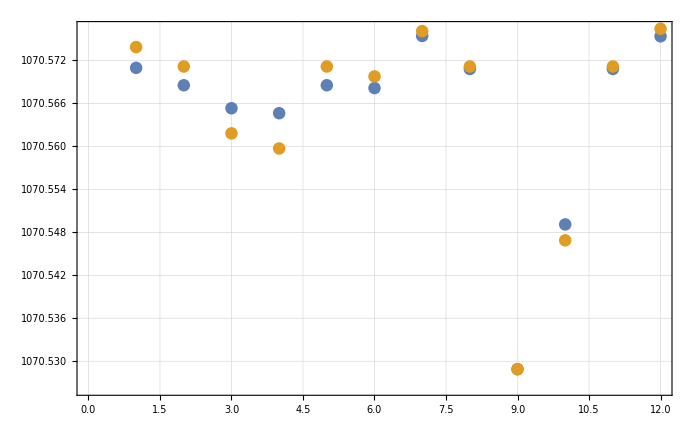

```mathematica
ListPlot[{Benchmarks2DIntpLimitsMinRec0[[All,1]],Benchmarks2DIntpLimitsMinRec1[[All,1]]}]
```

### time

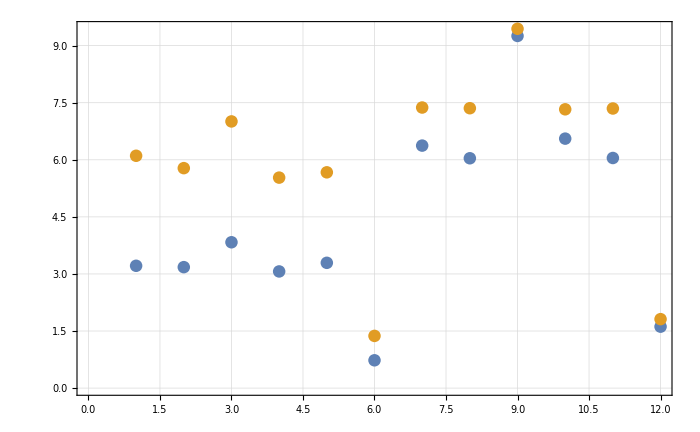

```mathematica
ListPlot[{Benchmarks2DIntpLimitsMinRec0[[All,3]],Benchmarks2DIntpLimitsMinRec1[[All,3]]}]
```

### samples

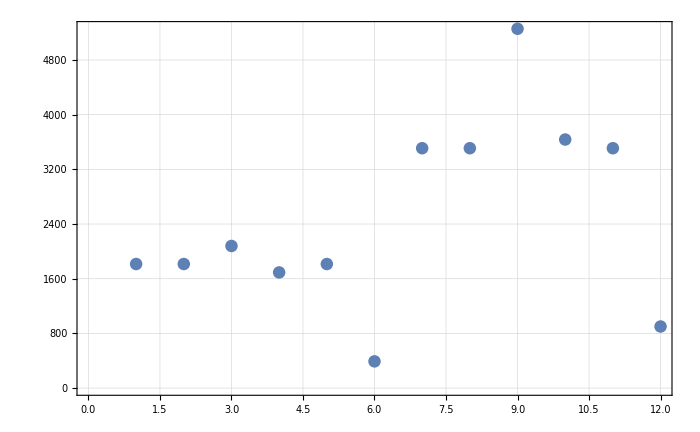

```mathematica
ListPlot[Length[#]&/@Benchmarks2DIntpLimitsMinRec0[[All,2]]]
```

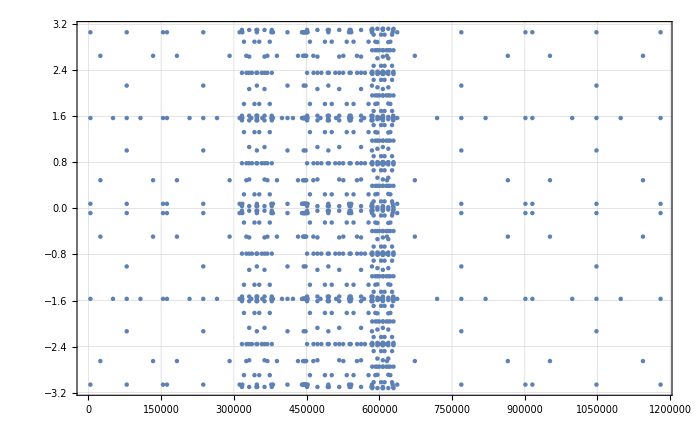

```mathematica
ListPlot[Benchmarks2DIntpLimits[[12,2]]]
```

## Without p limits

```mathematica
IntegrationBenchmark[Intopts_]:=Module[
{t0,t1,result,samples},
t0=AbsoluteTime[];
{result,{samples}}=
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVAndMomentumInt[0.,0.,0.,{0.,Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Intopts];
t1=AbsoluteTime[];
{result,samples,t1-t0}
]
```

```mathematica
Benchmarks2DIntMinRec0=IntegrationBenchmark[#]&/@IntOptionList[0]
```

{{1070.6,{{12924.4,-3.0732},{12924.4,-2.78679},{12924.4,-2.29384},{12924.4,-1.63079},{12924.4,-0.846795},{12924.4,0.},{12924.4,0.846795},{12924.4,1.63079},{12924.4,2.29384},4702,{454456.,-1.63079},{454456.,-0.846795},{454456.,0.},{454456.,0.846795},{454456.,1.63079},{454456.,2.29384},{454456.,2.78679},{454456.,3.0732}},7.744961},10,{1}}
 |  |  |  |

### 432s

```mathematica
Benchmarks2DIntMinRec1=IntegrationBenchmark[#]&/@IntOptionList[1]
```

{1}
 |  |  |  |

### took 473s

```mathematica
Grid[Join[{{"Index","Method","MinRec0, Result","Time (s)","MinRec1, Result","Time (s)"}},Table[{i,IntOptionList[0][[i,1,2,1]]<>IntOptionList[0][[i,1,2,2,2]],Benchmarks2DIntMinRec0[[i,1]],Benchmarks2DIntMinRec0[[i,3]],Benchmarks2DIntMinRec1[[i,1]],Benchmarks2DIntMinRec1[[i,3]]},{i,1,12}]],Frame->All]
```

Index | Method | MinRec0, Result | Time (s) | MinRec1, Result | Time (s)
1 | GlobalAdaptiveGaussBerntsenEspelidRule | 1070.6 | 7.744961 | 1070.6 | 15.48768
2 | GlobalAdaptiveGaussKronrodRule | 1070.55 | 6.800007 | 1070.55 | 13.35353
3 | GlobalAdaptiveLobattoKronrodRule | 1070.72 | 5.509745 | 1070.72 | 10.87123
4 | GlobalAdaptiveClenshawCurtisRule | 1070.56 | 5.588253 | 1070.56 | 12.88936
5 | GlobalAdaptiveCartesianRule | 1070.55 | 6.853849 | 1070.55 | 13.4996
6 | GlobalAdaptiveMultidimensionalRule | 1070.61 | 1.32308 | 1070.62 | 2.86318
7 | LocalAdaptiveGaussBerntsenEspelidRule | 1070.31 | 87.191628 | 1070.31 | 86.854721
8 | LocalAdaptiveGaussKronrodRule | 1070.74 | 102.19877 | 1070.74 | 102.94649
9 | LocalAdaptiveLobattoKronrodRule | 1070.15 | 58.233721 | 1070.15 | 59.688305
10 | LocalAdaptiveClenshawCurtisRule | 1072.11 | 37.415553 | 1072.11 | 38.240904
11 | LocalAdaptiveCartesianRule | 1070.74 | 101.59471 | 1070.74 | 104.95192
12 | LocalAdaptiveMultidimensionalRule | 1071.56 | 9.781038 | 1071.56 | 9.764935

### int value

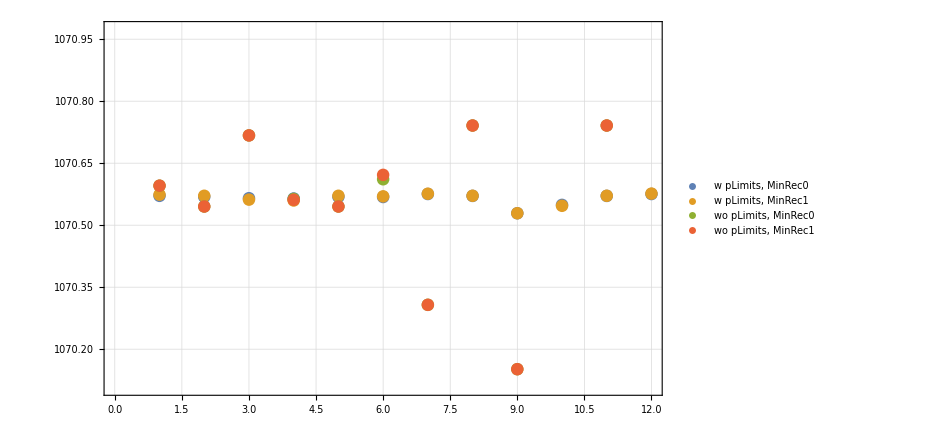

```mathematica
ListPlot[{Benchmarks2DIntpLimitsMinRec0[[All,1]],Benchmarks2DIntpLimitsMinRec1[[All,1]],Benchmarks2DIntMinRec0[[All,1]],Benchmarks2DIntMinRec1[[All,1]]},PlotLegends->{"w pLimits, MinRec0","w pLimits, MinRec1","wo pLimits, MinRec0","wo pLimits, MinRec1"}]
```

### time

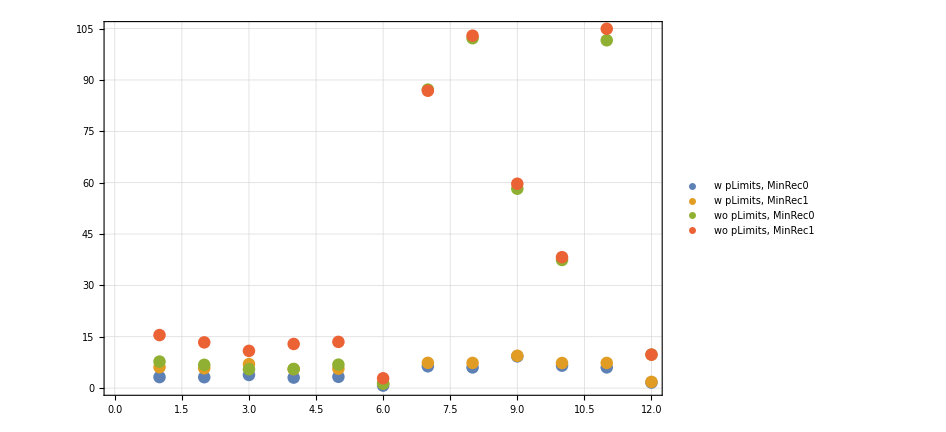

```mathematica
ListPlot[{Benchmarks2DIntpLimitsMinRec0[[All,3]],Benchmarks2DIntpLimitsMinRec1[[All,3]],Benchmarks2DIntMinRec0[[All,3]],Benchmarks2DIntMinRec1[[All,3]]},PlotLegends->{"w pLimits, MinRec0","w pLimits, MinRec1","wo pLimits, MinRec0","wo pLimits, MinRec1"}]
```

# Adding phiDet integration

```mathematica
Get["NeutronBeam/MethodTesting.m"];
```

Set::wrsym: Symbol pmax is Protected.

### Closed Int Rules are: Lobatto Kronod, Clenshaw Curtis, Trapez

```mathematica
IntegrationRules={"GaussBerntsenEspelidRule","GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule","CartesianRule","MultidimensionalRule"};
```

```mathematica
IntegrationStrategies={"GlobalAdaptive","LocalAdaptive"};
```

```mathematica
ClearAll[IntOptionList]
```

```mathematica
IntOptionList[MinRec_]=Flatten[Table[
{Method->{strategy,Method->rule},MinRecursion->MinRec,MaxRecursion->10},
{strategy,IntegrationStrategies},{rule,IntegrationRules}],1]
```

{{Method→{GlobalAdaptive,Method→GaussBerntsenEspelidRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→CartesianRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→GaussBerntsenEspelidRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→CartesianRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10}}

### we do this now without reap and sow. should be faster and we don’t really need the sample points

## With p X limits

```mathematica
IntegrationBenchmark3DpLimits[Intopts_]:=Module[
{t0,t1,result},
t0=AbsoluteTime[];
result=
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVMomentumPhiDetIntpLimits[0.,0.,0.,{Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Intopts];
t1=AbsoluteTime[];
{result,t1-t0}
]
```

### First, check a small selection for time estimates

```mathematica
Benchmarks3DIntpLimitsMinRec0=IntegrationBenchmark3DpLimits[IntOptionList[0][[6]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{8877.94,441.989552}

```mathematica
CheckTest=IntegrationBenchmark3DpLimits[{Method->"LocalAdaptive",MinRecursion->3,MaxRecursion->10}]
```

{8877.83,359.574145}

```mathematica
CheckTest2=IntegrationBenchmark3DpLimits[{Method->{"LocalAdaptive",Method->"MultidimensionalRule"},MinRecursion->3,MaxRecursion->10}]
```

{8877.83,332.62829}

```mathematica
CheckTest22=IntegrationBenchmark3DpLimits[{Method->{"LocalAdaptive",Method->"MultidimensionalRule"},MinRecursion->0,MaxRecursion->10}]
```

{8885.84,111.02198}

### very fast, but results are different above precision threshold

```mathematica
CheckTest3=IntegrationBenchmark3DpLimits[{Method->{"GlobalAdaptive",Method->"MultidimensionalRule"},MinRecursion->0,MaxRecursion->10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{8877.94,448.393224}

### result more in agreement with others, but takes longer!

### now MonteCarlo Test

```mathematica
CheckTest4=IntegrationBenchmark3DpLimits[{Method->"AdaptiveMonteCarlo",MinRecursion->3,MaxRecursion->10,MaxPoints->10000000}]
```

$Aborted

### aborted after 1478s

```mathematica
CloseKernels[]
```

{KernelObject[1,local,<defunct>],KernelObject[2,local,<defunct>],KernelObject[3,local,<defunct>],KernelObject[4,local,<defunct>],KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>],KernelObject[7,local,<defunct>]}

```mathematica
LaunchKernels[3]
```

{KernelObject[8,local],KernelObject[9,local],KernelObject[10,local]}

```mathematica
Benchmarks3DIntpLimitsMinRec0=ParallelMap[IntegrationBenchmark3DpLimits[#]&,IntOptionList[0]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{8877.95,6996.232034},{8877.94,4646.042707},{8877.96,3448.34682},{8877.95,4065.649037},{8877.94,4719.199587},{8877.94,272.27292},{8876.45,2851.43194},{8876.96,2385.11653},{8877.44,1442.28096},{8878.01,1650.18135},{8876.96,2366.32969},{8885.84,68.23987}}

```mathematica
$ConfiguredKernels
```

{LightweightGridClient`LightweightGrid[{Agent→http://193.170.93.100:3737/WolframRemoteServices,KernelCount→5,LocalLinkMode→Connect,Service→,Timeout→30}],«4 local kernels»}

```mathematica
LaunchKernels[LightweightGridClient`LightweightGrid[{"Agent"->"http://193.170.93.100:3737/WolframRemoteServices","KernelCount"->4,"LocalLinkMode"->"Connect","Service"->"","Timeout"->30}]]
```

{KernelObject[16,193.170.93.100],KernelObject[17,193.170.93.100],KernelObject[18,193.170.93.100],KernelObject[19,193.170.93.100]}

```mathematica
Kernels[]
```

{KernelObject[16,193.170.93.100],KernelObject[17,193.170.93.100],KernelObject[18,193.170.93.100],KernelObject[19,193.170.93.100]}

```mathematica
CloseKernels[]
```

{KernelObject[8,local,<defunct>],KernelObject[9,local,<defunct>],KernelObject[10,local,<defunct>],KernelObject[11,193.170.93.100,<defunct>],KernelObject[12,193.170.93.100,<defunct>],KernelObject[13,193.170.93.100,<defunct>],KernelObject[14,193.170.93.100,<defunct>],KernelObject[15,193.170.93.100,<defunct>]}

```mathematica
Benchmarks3DIntpLimitsMinRec1=ParallelMap[IntegrationBenchmark3DpLimits[#]&,IntOptionList[1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{8877.95,12913.42459},{8877.9,8679.178164},{8877.95,6342.967019},{8877.96,7450.313768},{8877.9,8835.073328},{8878.01,516.690569},{8876.45,2891.16563},{8876.96,2402.93414},{8877.44,1461.9916},{8878.01,1678.05212},{8876.96,2387.33607},{8877.83,124.55134}}

### took 53s with minrecursion 0. 72s for minrecursion 1

```mathematica
Grid[Join[{{"Index","Method","MinRec0, Result","Time (h)","MinRec1, Result","Time (h)"}},Table[{i,IntOptionList[0][[i,1,2,1]]<>IntOptionList[0][[i,1,2,2,2]],Benchmarks3DIntpLimitsMinRec0[[i,1]],Round[Benchmarks3DIntpLimitsMinRec0[[i,2]]/3600.,0.01],Benchmarks3DIntpLimitsMinRec1[[i,1]],Round[Benchmarks3DIntpLimitsMinRec1[[i,2]]/3600.,0.01]},{i,1,12}]],Frame->All]
```

Index | Method | MinRec0, Result | Time (h) | MinRec1, Result | Time (h)
1 | GlobalAdaptiveGaussBerntsenEspelidRule | 8877.95 | 1.94 | 8877.95 | 3.59
2 | GlobalAdaptiveGaussKronrodRule | 8877.94 | 1.29 | 8877.9 | 2.41
3 | GlobalAdaptiveLobattoKronrodRule | 8877.96 | 0.96 | 8877.95 | 1.76
4 | GlobalAdaptiveClenshawCurtisRule | 8877.95 | 1.13 | 8877.96 | 2.07
5 | GlobalAdaptiveCartesianRule | 8877.94 | 1.31 | 8877.9 | 2.45
6 | GlobalAdaptiveMultidimensionalRule | 8877.94 | 0.08 | 8878.01 | 0.14
7 | LocalAdaptiveGaussBerntsenEspelidRule | 8876.45 | 0.79 | 8876.45 | 0.8
8 | LocalAdaptiveGaussKronrodRule | 8876.96 | 0.66 | 8876.96 | 0.67
9 | LocalAdaptiveLobattoKronrodRule | 8877.44 | 0.4 | 8877.44 | 0.41
10 | LocalAdaptiveClenshawCurtisRule | 8878.01 | 0.46 | 8878.01 | 0.47
11 | LocalAdaptiveCartesianRule | 8876.96 | 0.66 | 8876.96 | 0.66
12 | LocalAdaptiveMultidimensionalRule | 8885.84 | 0.02 | 8877.83 | 0.03

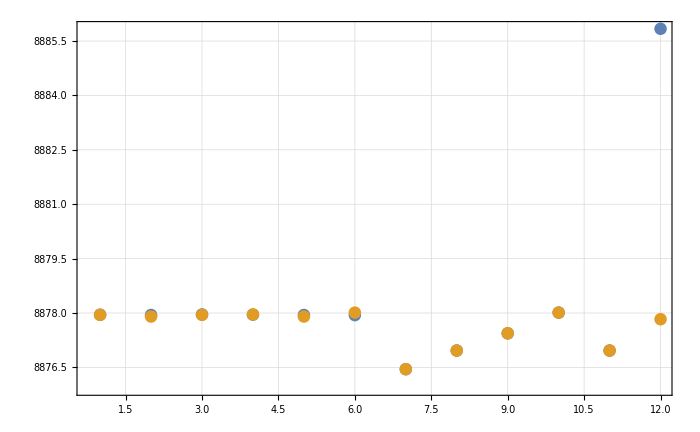

```mathematica
ListPlot[{Benchmarks3DIntpLimitsMinRec0[[All,1]],Benchmarks3DIntpLimitsMinRec1[[All,1]]},PlotRange->All]
```

```mathematica
Total[Benchmarks3DIntpLimitsMinRec0[[All,2]]]/3600.
```

9.69759

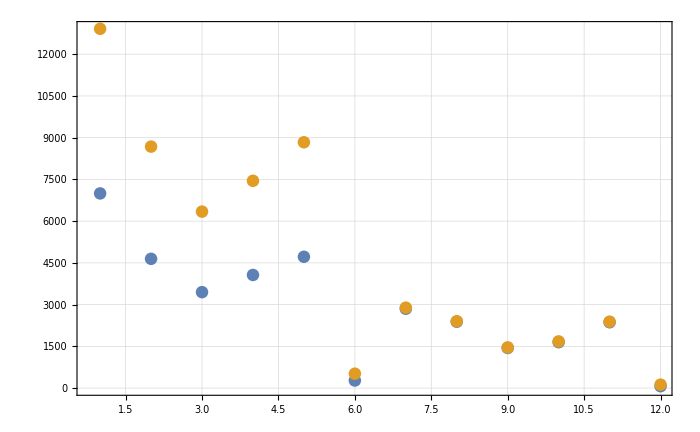

```mathematica
ListPlot[{Benchmarks3DIntpLimitsMinRec0[[All,2]],Benchmarks3DIntpLimitsMinRec1[[All,2]]},PlotRange->All]
```

## With ALL p limits

```mathematica
IntegrationRules2={(*"GaussBerntsenEspelidRule",*)"GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule",(*"CartesianRule",*)"MultidimensionalRule"};
```

```mathematica
IntegrationStrategies={"GlobalAdaptive","LocalAdaptive"};
```

```mathematica
ClearAll[IntOptionList]
```

```mathematica
IntOptionList2[MinRec_]=Flatten[Table[
{Method->{strategy,Method->rule},MinRecursion->MinRec,MaxRecursion->10},
{strategy,IntegrationStrategies},{rule,IntegrationRules2}],1]
```

{{Method→{GlobalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10}}

```mathematica
IntegrationBenchmark3DpLimitsAll[Intopts_]:=Module[
{t0,t1,result},
t0=AbsoluteTime[];
result=
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVMomentumPhiDetIntpLimitsAll[0.,0.,0.,{Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Intopts];
t1=AbsoluteTime[];
{result,t1-t0}
]
```

```mathematica
$ConfiguredKernels
```

{LightweightGridClient`LightweightGrid[{Agent→http://193.170.93.100:3737/WolframRemoteServices,KernelCount→5,LocalLinkMode→Connect,Service→,Timeout→30}],«4 local kernels»}

```mathematica
LaunchKernels[LightweightGridClient`LightweightGrid[{"Agent"->"http://193.170.93.100:3737/WolframRemoteServices","KernelCount"->4,"LocalLinkMode"->"Connect","Service"->"","Timeout"->30}]]
```

{KernelObject[1,193.170.93.100],KernelObject[2,193.170.93.100],KernelObject[3,193.170.93.100],KernelObject[4,193.170.93.100]}

```mathematica
Kernels[]
```

{KernelObject[1,193.170.93.100],KernelObject[2,193.170.93.100],KernelObject[3,193.170.93.100],KernelObject[4,193.170.93.100]}

```mathematica
CloseKernels[]
```

{}

```mathematica
Benchmarks3DIntpLimitsMinRec0Allp=ParallelMap[IntegrationBenchmark3DpLimitsAll[#]&,IntOptionList2[0]]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[35853@193.170.93.100,46873@193.170.93.100,304,7].

Kernels::rdead: Subkernel connected through KernelObject[1,193.170.93.100] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {4} assigned to KernelObject[1,193.170.93.100,<defunct>].

LinkObject::linkn: Argument LinkObject[35853@193.170.93.100,46873@193.170.93.100,304,7] in LinkClose[LinkObject[35853@193.170.93.100,46873@193.170.93.100,304,7]] has an invalid LinkObject number; the link may be closed.

OptionValue::nodef: Unknown option KernelSpeed for LightweightGridClient`RemoteKernelOpen.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[1,193.170.93.100,<defunct>] resurrected as KernelObject[5,193.170.93.100].

NIntegrate::nlim: p = {0.01,-0.03,0.035,0.} is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject[37965@193.170.93.100,33473@193.170.93.100,307,10].

Kernels::rdead: Subkernel connected through KernelObject[4,193.170.93.100] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {3} assigned to KernelObject[4,193.170.93.100,<defunct>].

LinkObject::linkn: Argument LinkObject[37965@193.170.93.100,33473@193.170.93.100,307,10] in LinkClose[LinkObject[37965@193.170.93.100,33473@193.170.93.100,307,10]] has an invalid LinkObject number; the link may be closed.

LaunchKernels::clone: Kernel KernelObject[4,193.170.93.100,<defunct>] resurrected as KernelObject[6,193.170.93.100].

NIntegrate::nlim: p = {0.01,-0.03,0.035,0.} is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject[38319@193.170.93.100,39549@193.170.93.100,350,7].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[5,193.170.93.100] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {4} assigned to KernelObject[5,193.170.93.100,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject[38319@193.170.93.100,39549@193.170.93.100,350,7] in LinkClose[LinkObject[38319@193.170.93.100,39549@193.170.93.100,350,7]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[5,193.170.93.100,<defunct>] resurrected as KernelObject[7,193.170.93.100].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

NIntegrate::nlim: p = {0.01,-0.03,0.035,0.} is not a valid limit of integration.

$Aborted

```mathematica
Benchmarks3DIntpLimitsMinRec1=ParallelMap[IntegrationBenchmark3DpLimits[#]&,IntOptionList[1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{8877.95,12913.42459},{8877.9,8679.178164},{8877.95,6342.967019},{8877.96,7450.313768},{8877.9,8835.073328},{8878.01,516.690569},{8876.45,2891.16563},{8876.96,2402.93414},{8877.44,1461.9916},{8878.01,1678.05212},{8876.96,2387.33607},{8877.83,124.55134}}

### took 53s with minrecursion 0. 72s for minrecursion 1

```mathematica
Grid[Join[{{"Index","Method","MinRec0, Result","Time (h)","MinRec1, Result","Time (h)"}},Table[{i,IntOptionList[0][[i,1,2,1]]<>IntOptionList[0][[i,1,2,2,2]],Benchmarks3DIntpLimitsMinRec0[[i,1]],Round[Benchmarks3DIntpLimitsMinRec0[[i,2]]/3600.,0.01],Benchmarks3DIntpLimitsMinRec1[[i,1]],Round[Benchmarks3DIntpLimitsMinRec1[[i,2]]/3600.,0.01]},{i,1,12}]],Frame->All]
```

Index | Method | MinRec0, Result | Time (h) | MinRec1, Result | Time (h)
1 | GlobalAdaptiveGaussBerntsenEspelidRule | 8877.95 | 1.94 | 8877.95 | 3.59
2 | GlobalAdaptiveGaussKronrodRule | 8877.94 | 1.29 | 8877.9 | 2.41
3 | GlobalAdaptiveLobattoKronrodRule | 8877.96 | 0.96 | 8877.95 | 1.76
4 | GlobalAdaptiveClenshawCurtisRule | 8877.95 | 1.13 | 8877.96 | 2.07
5 | GlobalAdaptiveCartesianRule | 8877.94 | 1.31 | 8877.9 | 2.45
6 | GlobalAdaptiveMultidimensionalRule | 8877.94 | 0.08 | 8878.01 | 0.14
7 | LocalAdaptiveGaussBerntsenEspelidRule | 8876.45 | 0.79 | 8876.45 | 0.8
8 | LocalAdaptiveGaussKronrodRule | 8876.96 | 0.66 | 8876.96 | 0.67
9 | LocalAdaptiveLobattoKronrodRule | 8877.44 | 0.4 | 8877.44 | 0.41
10 | LocalAdaptiveClenshawCurtisRule | 8878.01 | 0.46 | 8878.01 | 0.47
11 | LocalAdaptiveCartesianRule | 8876.96 | 0.66 | 8876.96 | 0.66
12 | LocalAdaptiveMultidimensionalRule | 8885.84 | 0.02 | 8877.83 | 0.03

```mathematica
ListPlot[{Benchmarks3DIntpLimitsMinRec0[[All,1]],Benchmarks3DIntpLimitsMinRec1[[All,1]]},PlotRange->All]
```

-Graphics-

```mathematica
Total[Benchmarks3DIntpLimitsMinRec0[[All,2]]]/3600.
```

9.69759

```mathematica
ListPlot[{Benchmarks3DIntpLimitsMinRec0[[All,2]],Benchmarks3DIntpLimitsMinRec1[[All,2]]},PlotRange->All]
```

-Graphics-

## Without p limits

```mathematica
IntegrationBenchmark[Intopts_]:=Module[
{t0,t1,result,samples},
t0=AbsoluteTime[];
{result,{samples}}=
Int2DwNBeamCompiledManualphiAAllLimitsPhiDVAndMomentumInt[0.,0.,0.,{0.,Pi/4},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Intopts];
t1=AbsoluteTime[];
{result,samples,t1-t0}
]
```

```mathematica
Benchmarks2DIntMinRec0=IntegrationBenchmark[#]&/@IntOptionList[0]
```

{{1070.6,{{12924.4,-3.0732},{12924.4,-2.78679},{12924.4,-2.29384},{12924.4,-1.63079},{12924.4,-0.846795},{12924.4,0.},{12924.4,0.846795},{12924.4,1.63079},{12924.4,2.29384},4702,{454456.,-1.63079},{454456.,-0.846795},{454456.,0.},{454456.,0.846795},{454456.,1.63079},{454456.,2.29384},{454456.,2.78679},{454456.,3.0732}},7.744961},10,{1}}
 |  |  |  |

### 432s

```mathematica
Benchmarks2DIntMinRec1=IntegrationBenchmark[#]&/@IntOptionList[1]
```

{1}
 |  |  |  |

### took 473s

```mathematica
Grid[Join[{{"Index","Method","MinRec0, Result","Time (s)","MinRec1, Result","Time (s)"}},Table[{i,IntOptionList[0][[i,1,2,1]]<>IntOptionList[0][[i,1,2,2,2]],Benchmarks2DIntMinRec0[[i,1]],Benchmarks2DIntMinRec0[[i,3]],Benchmarks2DIntMinRec1[[i,1]],Benchmarks2DIntMinRec1[[i,3]]},{i,1,12}]],Frame->All]
```

Index | Method | MinRec0, Result | Time (s) | MinRec1, Result | Time (s)
1 | GlobalAdaptiveGaussBerntsenEspelidRule | 1070.6 | 7.744961 | 1070.6 | 15.48768
2 | GlobalAdaptiveGaussKronrodRule | 1070.55 | 6.800007 | 1070.55 | 13.35353
3 | GlobalAdaptiveLobattoKronrodRule | 1070.72 | 5.509745 | 1070.72 | 10.87123
4 | GlobalAdaptiveClenshawCurtisRule | 1070.56 | 5.588253 | 1070.56 | 12.88936
5 | GlobalAdaptiveCartesianRule | 1070.55 | 6.853849 | 1070.55 | 13.4996
6 | GlobalAdaptiveMultidimensionalRule | 1070.61 | 1.32308 | 1070.62 | 2.86318
7 | LocalAdaptiveGaussBerntsenEspelidRule | 1070.31 | 87.191628 | 1070.31 | 86.854721
8 | LocalAdaptiveGaussKronrodRule | 1070.74 | 102.19877 | 1070.74 | 102.94649
9 | LocalAdaptiveLobattoKronrodRule | 1070.15 | 58.233721 | 1070.15 | 59.688305
10 | LocalAdaptiveClenshawCurtisRule | 1072.11 | 37.415553 | 1072.11 | 38.240904
11 | LocalAdaptiveCartesianRule | 1070.74 | 101.59471 | 1070.74 | 104.95192
12 | LocalAdaptiveMultidimensionalRule | 1071.56 | 9.781038 | 1071.56 | 9.764935

```mathematica
ListPlot[{Benchmarks2DIntpLimitsMinRec0[[All,1]],Benchmarks2DIntpLimitsMinRec1[[All,1]],Benchmarks2DIntMinRec0[[All,1]],Benchmarks2DIntMinRec1[[All,1]]},PlotLegends->{"w pLimits, MinRec0","w pLimits, MinRec1","wo pLimits, MinRec0","wo pLimits, MinRec1"}]
```

-Graphics-

```mathematica
ListPlot[{Benchmarks2DIntpLimitsMinRec0[[All,3]],Benchmarks2DIntpLimitsMinRec1[[All,3]],Benchmarks2DIntMinRec0[[All,3]],Benchmarks2DIntMinRec1[[All,3]]},PlotLegends->{"w pLimits, MinRec0","w pLimits, MinRec1","wo pLimits, MinRec0","wo pLimits, MinRec1"}]
```

-Graphics-

# All Integrations (inc th0)

```mathematica
Get["NeutronBeam/MethodTesting.m"];
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
IntegrationRules2={(*"GaussBerntsenEspelidRule",*)"GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule",(*"CartesianRule",*)"MultidimensionalRule"};
```

```mathematica
IntegrationStrategies={"GlobalAdaptive","LocalAdaptive"};
```

```mathematica
ClearAll[IntOptionList]
```

```mathematica
IntOptionList2[MinRec_]=Flatten[Table[
{Method->{strategy,Method->rule},MinRecursion->MinRec,MaxRecursion->10},
{strategy,IntegrationStrategies},{rule,IntegrationRules2}],1]
```

{{Method→{GlobalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{GlobalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→GaussKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→LobattoKronrodRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→ClenshawCurtisRule},MinRecursion→MinRec,MaxRecursion→10},{Method→{LocalAdaptive,Method→MultidimensionalRule},MinRecursion→MinRec,MaxRecursion→10}}

## With p X limits

```mathematica
IntegrationBenchmark4DpXLimits[yD_,xD_,Intopts_]:=Module[
{t0,t1,result},
t0=AbsoluteTime[];
result=
Int2DwNBeamCompiledManualphiAAllIntpXLimits[0.,yD,xD,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Intopts];
t1=AbsoluteTime[];
{result,t1-t0}
]
```

```mathematica
$ConfiguredKernels
```

{LightweightGridClient`LightweightGrid[{Agent→http://193.170.93.100:3737/WolframRemoteServices,KernelCount→5,LocalLinkMode→Connect,Service→,Timeout→30}],«4 local kernels»}

```mathematica
CloseKernels[]
```

{KernelObject[5,193.170.93.100,<defunct>],KernelObject[6,193.170.93.100,<defunct>],KernelObject[7,193.170.93.100,<defunct>],KernelObject[8,193.170.93.100,<defunct>],KernelObject[9,193.170.93.100,<defunct>],KernelObject[10,local,<defunct>],KernelObject[11,local,<defunct>],KernelObject[12,local,<defunct>],KernelObject[13,local,<defunct>]}

```mathematica
LaunchKernels[LightweightGridClient`LightweightGrid[{"Agent"->"http://193.170.93.100:3737/WolframRemoteServices","KernelCount"->4,"LocalLinkMode"->"Connect","Service"->"","Timeout"->30}]]
```

{KernelObject[14,193.170.93.100],KernelObject[15,193.170.93.100],KernelObject[16,193.170.93.100],KernelObject[17,193.170.93.100]}

### run on home pc

```mathematica
TestInt = 
 IntegrationBenchmark4DpXLimits[{Method -> {"LocalAdaptive", 
     Method -> "ClenshawCurtisRule"}, MinRecursion -> 0}]
```

```mathematica
{3954.78,27384.8111145}
```

```mathematica
TestInt2 = 
 IntegrationBenchmark4DpXLimits[{Method -> {"LocalAdaptive", 
     Method -> "MultidimensionalRule"}, MinRecursion -> 0}]
```

{3953.91,781.753515}

```mathematica
TestInt2pLimitsXY = 
 IntegrationBenchmark4DpXLimits[0.015,0.015,{Method -> {"LocalAdaptive", 
     Method -> "MultidimensionalRule"}, MinRecursion -> 0}]
```

{1798.5,488.914752}

```mathematica
TestInt3 = 
 IntegrationBenchmark4DpXLimits[{Method -> {"GlobalAdaptive", 
     Method -> "MultidimensionalRule"}, MinRecursion -> 0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3951.38 and 21.9881 for the integral and error estimates.

{3951.38,1832.80856}

```mathematica
TestInt4 = 
 IntegrationBenchmark4DpXLimits[{Method ->"AdaptiveMonteCarlo", MinRecursion -> 0,MaxPoints->10^7}]
```

{3948.14,7063.298217}

### MC doesnt seem to make much sense. now check, if higher Minrecursion takes up more time?

```mathematica
TestInt5 = 
 IntegrationBenchmark4DpXLimits[{Method -> {"LocalAdaptive", 
     Method -> "MultidimensionalRule"}, MinRecursion -> 3}]
```

$Aborted

```mathematica
Kernels[]
```

{KernelObject[14,193.170.93.100],KernelObject[15,193.170.93.100],KernelObject[16,193.170.93.100],KernelObject[17,193.170.93.100]}

```mathematica
Benchmarks4DIntpXLimitsMinRec0=ParallelMap[IntegrationBenchmark4DpXLimits[#]&,IntOptionList2[0]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Benchmarks4DIntpXLimitsMinRec2=ParallelMap[IntegrationBenchmark4DpXLimits[#]&,IntOptionList2[2]]
```

## without p X limits

```mathematica
IntegrationBenchmark4D[yD_,xD_,Intopts_]:=Module[
{t0,t1,result},
t0=AbsoluteTime[];
result=
Int2DwNBeamCompiledManualphiAAllInt[0.,yD,xD,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,Intopts];
t1=AbsoluteTime[];
{result,t1-t0}
]
```

```mathematica
TestIntwoPLimits = IntegrationBenchmark4D[{Method -> {"LocalAdaptive", Method -> "MultidimensionalRule"}, MinRecursion -> 0}]
```

{3953.91,787.696921}

```mathematica
TestIntwoPLimits2 = IntegrationBenchmark4D[{Method -> "LocalAdaptive", MinRecursion -> 3, MaxRecursion->10}]
```

{3953.91,786.781236}

```mathematica
TestIntwoPLimits3XY = IntegrationBenchmark4D[0.015,0.015,{Method -> {"LocalAdaptive", Method -> "MultidimensionalRule"}, MinRecursion -> 0}]
```

{1798.5,491.042261}

```mathematica
TestIntwoPLimits3 =Int2DwNBeamCompiledManualphiAAllInt[0.,0.,0.,{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4,{Method -> "LocalAdaptive", MinRecursion -> 3, MaxRecursion->10}];
```

$Aborted

```mathematica
Needs["Integration`NIntegrateUtilities`"]
```

```mathematica
iRegionMethods={"Axis",(*"Boundaries",*)"Dimension","Error","GetRule"(*,"Integral","Integrand","WorkingPrecision"*)}
```

{Axis,Dimension,Error,GetRule}

### below took 783s

### it takes multidimensional rule

```mathematica
(*test=Reap[
NIntegrate[
ManualphiAIntegrandAllLimits[0.,0.,0.,{phiDV,phiDet,p,th0},
{Pi,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],
{th0,0.,thetamax[2.]},{phiDet,-Pi//N,Pi//N},{p,0.,pmax},{phiDV,-Pi//N,Pi//N},
PrecisionGoal->4,Method->"LocalAdaptive",AccuracyGoal->5,MinRecursion->3,MaxRecursion->10,
IntegrationMonitor:>Function[{iregs},Sow[Association/@Transpose[Map[Thread[#->Through[iregs[#]]]&,iRegionMethods]]]]
]
]*)
```

```mathematica
Benchmarks4DIntMinRec0=ParallelMap[IntegrationBenchmark4D[#]&,IntOptionList2[0]]
```

### check diff to previous integrand without p limits and why it is that much faster

```mathematica
Get["NeutronBeam/NBeam_IntTables.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
LaunchKernels[]
```

{KernelObject[5,193.170.93.100],KernelObject[6,193.170.93.100],KernelObject[7,193.170.93.100],KernelObject[8,193.170.93.100],KernelObject[9,193.170.93.100],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local]}

### all available kernels launched, don’t know how much parallelism of NIntegrate is there

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
Int2DwNBeamCompiledManualphiAAllLimits[0.,{{0.,0.}},{Pi,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.0,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},4]
t1=AbsoluteTime[];
t1-t0
```

Wed 11 Mar 2020 15:11:34

{3953.91}

544.979604

```mathematica
ParallelTable[

NIntegrate[ManualphiAIntegrandAllLimits[b,XYData[[bin,2]],XYData[[bin,1]],{phiDV,phiDet,p,th0},
{alpha,BRxB,rRxB,rA,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff}],
{th0,0.,thetamax[rF]},{phiDet,-Pi//N,Pi//N},{p,0.,pmax},{phiDV,-Pi//N,Pi//N},PrecisionGoal->IntPrec,Method->"LocalAdaptive",AccuracyGoal->5,MinRecursion->3,MaxRecursion->10],

{bin,1,Length[XYData]},Method->"FinestGrained"]
```

```mathematica
NIntegrate[ManualphiAIntegrandAllLimits[b,yD,xD,{phiDV,phiDet,p,th0},
{alpha,BRxB,rRxB,rA,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff}],
{th0,0.,thetamax[rF]},{phiDet,-Pi//N,Pi//N},{p,0.,pmax},{phiDV,-Pi//N,Pi//N},PrecisionGoal->IntPrec,AccuracyGoal->5,Sequence@Intopts]
```